## Объявление глобальных переменных

```mathematica
SetDirectory["/Users/kirillivanov/Documents/Code/For Geant analysis/a-w_g-xe/"]
print@x_:=(Print@x;x);
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

/Users/kirillivanov/Documents/Code/For Geant analysis/a-w_g-xe

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 10.2953 | 0.113121
1000. | 0. | 21.922 | 0.170191
2000. | 0. | 44.9594 | 0.240413
3000. | 0. | 68.2365 | 0.287832
4000. | 0. | 90.9245 | 0.357762
5000. | 0. | 114.259 | 0.379237
6000. | 0. | 137.248 | 0.42345
7000. | 0. | 160.12 | 0.450236
8000. | 0. | 182.424 | 0.483863
9000. | 0. | 205.693 | 0.53179
10000. | 0. | 229.012 | 0.534607

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-1.19182+0.0231229 x-1.32817×10^-8 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.19182 | 0.216029 | -5.51693 | 0.000562413
x | 0.0231229 | 0.0000999719 | 231.294 | 1.36669×10^-16
x^2 | -1.32817×10^-8 | 9.42445×10^-9 | -1.40929 | 0.196416

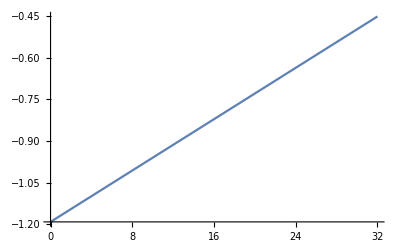

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

{-0.0710036,0.00419709,-0.0414616,0.17914,-0.162773,0.168128,0.180954,0.10207,-0.516948,-0.145655,0.303352}

{0.113121,0.170191,0.240413,0.287832,0.357762,0.379237,0.42345,0.450236,0.483863,0.53179,0.534607}

{0.39398,0.000608169,0.0297424,0.387351,0.207003,0.196544,0.182613,0.0513942,1.14143,0.0750185,0.321977}

0.373458

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

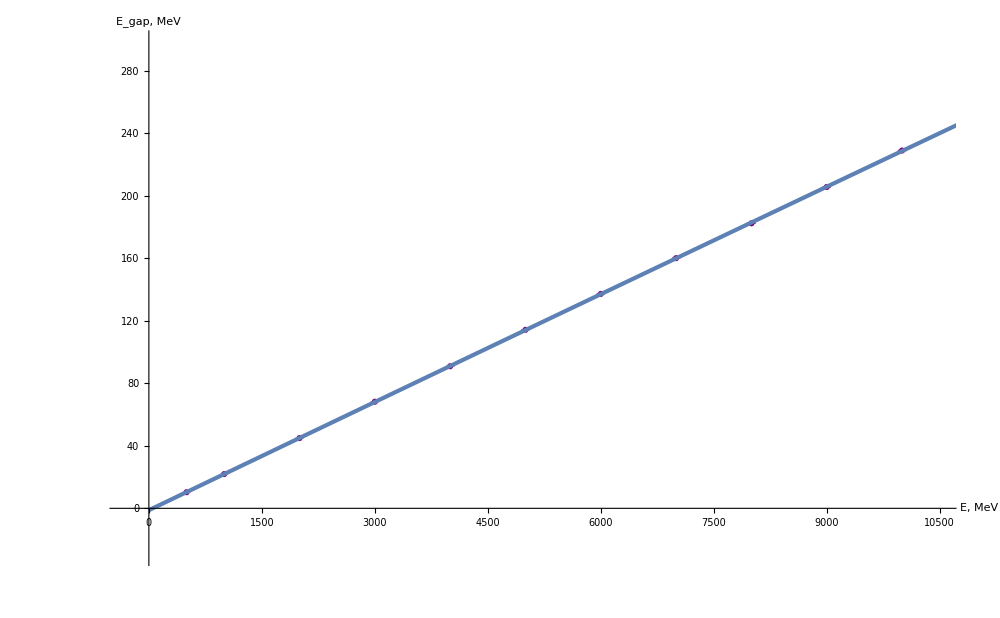

images/png/calib2.png

images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,299}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["images/png/calib2.png",plot2,"PNG"]
Export["images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
Export["fit_res2.csv",exportE,"CSV"]
```

{{-1.19182,0.0231229,-1.32817×10^-8},{0.216029,0.0000999719,9.42445×10^-9},0.373458}

fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
874.947 | 9.09894 | 0.237904 | 0.00509823
1353.98 | 10.7992 | 0.194524 | 0.00393827
1936.55 | 13.4613 | 0.166905 | 0.00329701
2935.06 | 16.3494 | 0.132356 | 0.00253752
3537.75 | 17.9593 | 0.126567 | 0.00240272
4175.17 | 18.2058 | 0.109006 | 0.00204878
5048.09 | 21.2495 | 0.105771 | 0.00198257
6340.63 | 23.5856 | 0.0924883 | 0.00172522
7163.92 | 23.395 | 0.0894367 | 0.00165882
8024.46 | 28.0672 | 0.0847539 | 0.00157775
9707.9 | 29.9498 | 0.0761233 | 0.00141925

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.0075177+6.86425/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0075177 | 0.00209043 | 3.59625 | 0.00578207
1/(√x) | 6.86425 | 0.109846 | 62.4898 | 3.47135×10^-13

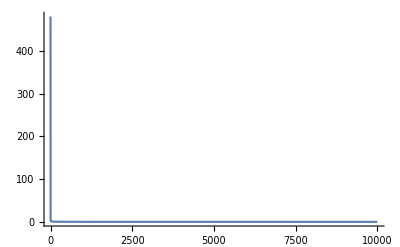

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

{-0.00167459,0.000460477,0.00340366,-0.00186376,0.00364345,-0.00474399,0.00164169,-0.00123325,0.00081963,0.000608604,-0.00106192}

{0.00509823,0.00393827,0.00329701,0.00253752,0.00240272,0.00204878,0.00198257,0.00172522,0.00165882,0.00157775,0.00141925}

{0.107889,0.0136711,1.06574,0.539463,2.29943,5.36164,0.68569,0.510992,0.24414,0.148797,0.559841}

1.28192

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

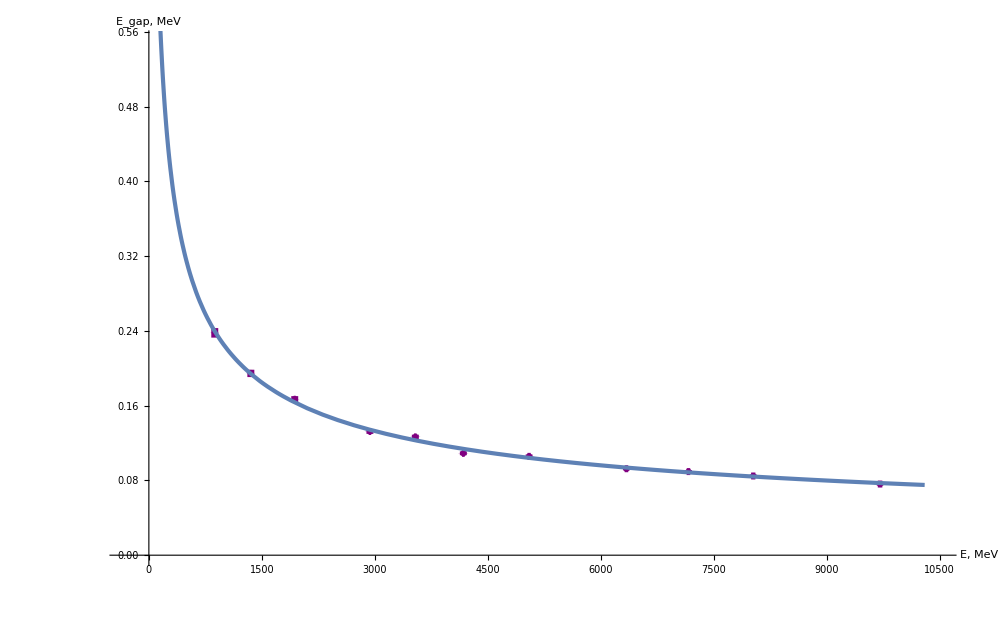

images/png/re.png

images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.55}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["images/png/re.png",plotR,"PNG"]
Export["images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
Export["fit_re_res.csv",exportR,"CSV"]
```

{{0.0075177,6.86425},{0.00209043,0.109846},1.28192}

fit_re_res.csv